## Routing a robot to collect data from n underwater sensors in mimum time Srikanth K.V.S. and Aaron T. Becker

### Set up a simulation

```mathematica
n=50;
edgeLenInm= 1;
p=RandomReal[edgeLenInm,{n,2}];
{dist,route}=FindShortestTour[p];
```

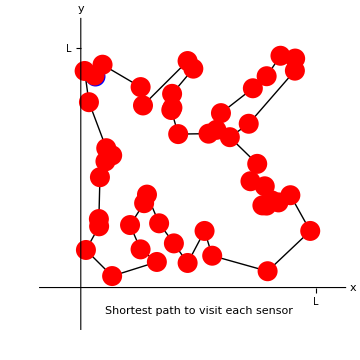
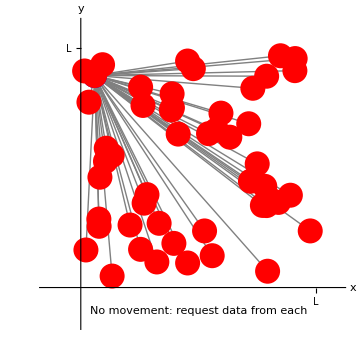

```mathematica
pr = {{-.15edgeLenInm,1.1 edgeLenInm},{-.15edgeLenInm,1.1 edgeLenInm}};
{Plot[{},{t,0,10},PlotRange->pr,
ImageSize->Medium,
AxesLabel->{"x","y"},Ticks->{{{edgeLenInm,"L"}},{{edgeLenInm,"L"}}},
AspectRatio->1,Epilog-> {PointSize[0.04],Blue,Point[p⟦1⟧],
Black,Text["Shortest path to visit each sensor",{edgeLenInm/2,-.1edgeLenInm}],
(*Line[p⟦route⟧]*)
Table[ Arrow[{p⟦route⟦j-1⟧⟧,p⟦route⟦j⟧⟧}],{j, 2, Length[route]}],PointSize[Medium],Red,Point[p]
}],
Plot[{},{t,0,10},PlotRange->{{-.15edgeLenInm,1.1 edgeLenInm},{-.15edgeLenInm,1.1 edgeLenInm}},
ImageSize->Medium,
AxesLabel->{"x","y"},Ticks->{{{edgeLenInm,"L"}},{{edgeLenInm,"L"}}},
AspectRatio->1,Epilog-> {Gray,Table[ Arrow[{p⟦1⟧,p⟦j⟧}],{j, 2, Length[p]}],
Black,
Text["No movement: request data from each",{edgeLenInm/2,-.1edgeLenInm}],
PointSize[0.05],Blue,Point[p⟦1⟧],Black,
PointSize[Medium],Red,Point[p]
}]}
```

### Models for communication. We have a Magnetic induction transmitter and an Acoutic transmitter The models below are made up. Miao Pan has data. I want bits per second as a function of distance

```mathematica
bitsPerSecMagneticInduc[dist_]:= 20 ⅇ^(-1/10dist)
bitsPerSecAccoustic[dist_]:= 2 ⅇ^(-1/100 dist)
```

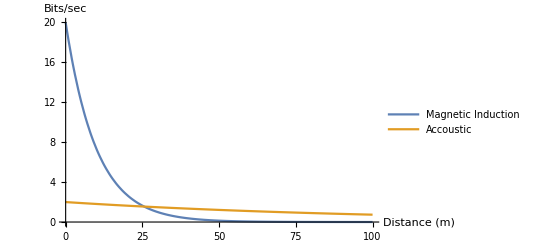

```mathematica
Plot[{bitsPerSecMagneticInduc[dist],bitsPerSecAccoustic[dist]},{dist,0,100},PlotRange->All,AxesLabel->{"Distance (m)","Bits/sec"},PlotLegends->{"Magnetic Induction","Accoustic"}]
```

### Calculate the total time to collect the data. Assume sensor i has Data[[i]] in bits.

```mathematica
maxVelmps = 1; (*robot max velocity in meters/s*)
Bts = 10;
DataInEachSensorBits[Bts_] := ConstantArray[Bts,n-1];
distToCommEachNode=Table[ EuclideanDistance[p⟦1⟧,p⟦j⟧],{j, 2, Length[p]}];
distToVisitEachNode=Table[ EuclideanDistance[p⟦route⟦j-1⟧⟧,p⟦route⟦j⟧⟧],{j, 2, Length[route]}];
(*time is distance*velocity + sum(bits*communicate[distance])   *)
totalTimeVisitEachNode[edgeLen_]:= edgeLen*Total[distToVisitEachNode]/maxVelmps + Total[DataInEachSensorBits[Bts]]/bitsPerSecMagneticInduc[0];
totalTimeCommEachNode[edgeLen_]:=  + Total[DataInEachSensorBits[Bts]/bitsPerSecAccoustic[distToCommEachNode*edgeLen]];
```

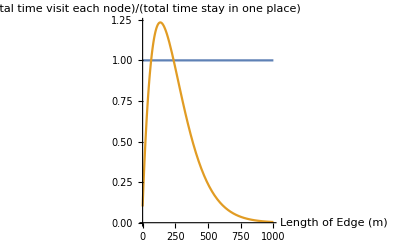

```mathematica
Plot[{1,totalTimeVisitEachNode[edgeLenInm]/totalTimeCommEachNode[edgeLenInm]},{edgeLenInm,0,1000},PlotRange->All,AxesLabel->{"Length of Edge (m)","(total time visit each node)/(total time stay in one place)"}]
```

### What about moving to the middle, then doing the scan? I think this means we need to communicate while we move.

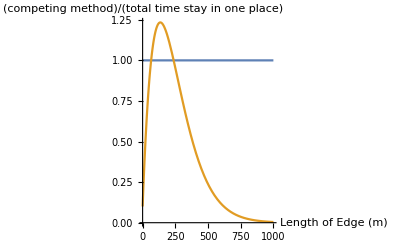

```mathematica
distFromMean=Table[ EuclideanDistance[Mean[p],p⟦j⟧],{j, 2, Length[p]}];
distMinStartAndMean =Min[#]&/@Transpose[{distToCommEachNode,distFromMean}];
totalTimeCommMin[edgeLen_]:=
edgeLen*2*EuclideanDistance[Mean[p],p⟦1⟧] +Total[DataInEachSensorBits/bitsPerSecAccoustic[distMinStartAndMean*edgeLen]]
Plot[{1,totalTimeVisitEachNode[edgeLenInm]/totalTimeCommEachNode[edgeLenInm],totalTimeCommMin[edgeLenInm]/totalTimeCommEachNode[edgeLenInm]},{edgeLenInm,0,1000},PlotRange->All,AxesLabel->{"Length of Edge (m)","(competing method)/(total time stay in one place)"}]
```

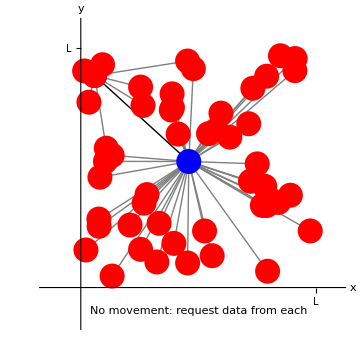

```mathematica
Plot[{},{t,0,10},PlotRange->{{-.15edgeLenInm,1.1 edgeLenInm},{-.15edgeLenInm,1.1 edgeLenInm}},
ImageSize->Medium,
AxesLabel->{"x","y"},Ticks->{{{edgeLenInm,"L"}},{{edgeLenInm,"L"}}},
AspectRatio->1,Epilog-> {Gray,Table[ Arrow[If[EuclideanDistance[p⟦1⟧,p⟦j⟧]<EuclideanDistance[Mean[p],p⟦j⟧],{p⟦1⟧,p⟦j⟧},{Mean[p],p⟦j⟧}]],{j, 2, Length[p]}],
Black,Arrow[{p⟦1⟧,Mean[p]}],
Text["No movement: request data from each",{edgeLenInm/2,-.1edgeLenInm}],
PointSize[0.05],Blue,Point[{p⟦1⟧,Mean[p]}],Black,
PointSize[Medium],Red,Point[p]
}]
```

### Ideas for finding good waypoints

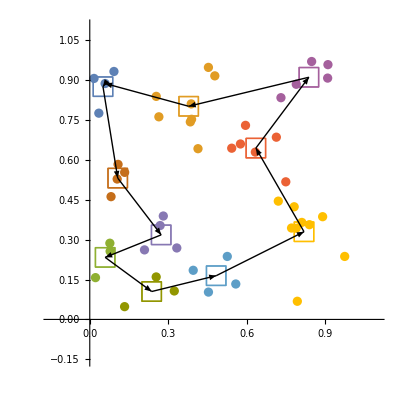

```mathematica
cl=FindClusters[p,10];
clusterMeans= Mean/@cl;
pathpts=Prepend[clusterMeans,p⟦1⟧];
{distCl,routeCl}=FindShortestTour[pathpts];

clPlot1=ListPlot[cl,AspectRatio->1];
clPlot2=ListPlot[Transpose[{clusterMeans}],AspectRatio->1,PlotMarkers->{□,20},PlotRange->pr,Epilog-> {Table[ Arrow[{pathpts⟦routeCl⟦j-1⟧⟧,pathpts⟦routeCl⟦j⟧⟧}],{j, 2, Length[routeCl]}]}];
Show[{clPlot2,clPlot1}]
```